now with a0-depending focusing lens of target

50.

0.00005

0.360025

2500.

1.×10^-8

wz^2/8*Dz

N::precsm: Requested precision -2 is smaller than $MinPrecision. Using $MinPrecision instead.

2500.

maximum denting Dstart in focus:

0.00005

0.00005 (1/((1+3.1272 u^2)^1.))^0.5

focal length inwards

(1250. (1.×10^-8 (1/((1+3.1272 u^2)^1.))^1.+0.000144 (1+3.1272 u^2)^1.))/((1/((1+3.1272 u^2)^1.))^0.5)

focal length outwards

-(1250. (1.×10^-8 (1/((1+3.1272 u^2)^1.))^1.+0.000144 (1+3.1272 u^2)^1.))/((1/((1+3.1272 u^2)^1.))^0.5)

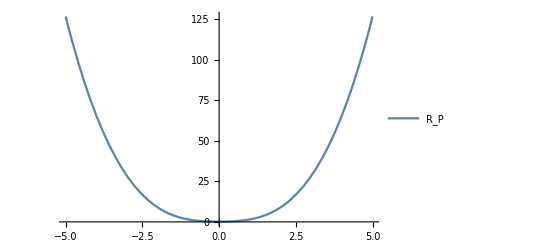

new focal position at

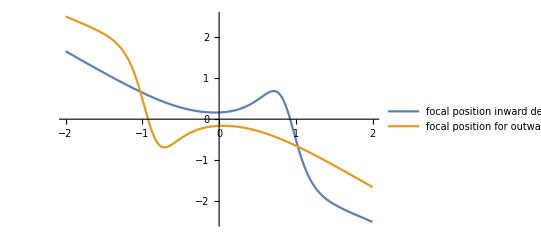

new beamwaist w0'

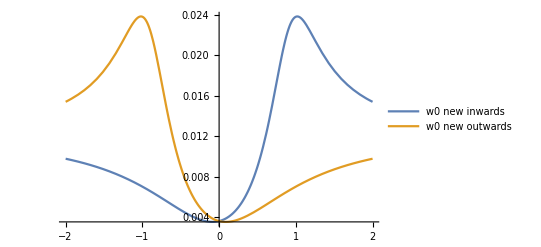

```mathematica
"now with a0-depending focusing lens of target"

$MaxExtraPrecision
w0 = 0.012;

lambdaL = 0.0008;
q = w0^2*π/(lambdaL);
D0 = 0.00005
R = (4*(D0^2)+(0.012^2))/(8*D0)
Print[1/(8*D0)]
Print[4*D0^2]

zr =  π*(w0^2)/lambdaL;
wz =  w0*(1+(u/zr)^2)^0.5;
"wz^2/8*Dz"
N[1/(8*D0), u=-2]

Clear[u, wz]
wz =  w0*(1+(u/zr)^2)^0.5;
"maximum denting Dstart in focus:"
Dstart = 0.00005
D100=Dstart*(w0^2/wz^2)^0.5

R100= (4*(D100^2)+(wz^2))/(8*D100);
"focal length inwards"
f1= R100/2

"focal length outwards"
fout= -R100/2

AA= (((q^2)/f1) - u*(1-u/f1));
BB= ((q^2/f1^2)+(1-u/f1)^2);
A= (((q^2)/fout) - u*(1-u/fout));
B = ((q^2/fout^2)+(1-u/fout)^2);
vin= AA/BB;
vpositive= A/B;

Plot[{f1}, {u, -5,5}, PlotLegends->{"R_P", "w(z)"}]



"new focal position at"
Plot[{vin, vpositive}, {u, -2,2}, PlotLegends->{"focal position inward denting", "focal position for outward denting"}]

wnew =w0* √((1-vin/f1)^2+(1/q^2)*(u+vin*(1-(u/f1)))^2);

woutward =√(w0^2*((1-vpositive/fout)^2+(1/q^2)*(u+vpositive*(1-(u/fout)))^2));
"new beamwaist w0'"
Plot[{wnew, woutward}, {u, -2, 2}, PlotLegends->{"w0 new inwards ", "w0 new outwards"}, PlotRange->All]
Clear[vin, R100, wnew, woutward, AA, BB, A, B, f1, fout, zr, q,  D100, vpositive,wz, u, Dstart]
```